# The QEC API Redesign: What Changed and Why

This note walks through, with runnable examples, everything that changed in the QEC layer in response to the API audit (QEC-API-Audit-and-Redesign.md). The plan that was followed, with its steps and the status of every observation, is QEC-API-Redesign-Plan.md; this note is the same work seen running.

The idea in one sentence: the mathematics did not change, the face did. The 593 tests that existed at the start passed after every step, and there are now 687. What changed is how the layer is asked things: through the objects the rest of the framework uses (QuantumOperator, QuantumChannel, QuantumMeasurementOperator, QuantumCircuitOperator), with one return type per function, and with fewer public names.

| step | what was done
       | 1 | three small fixes the audit asked for
       | 2 | the gadgets hand back framework circuits
       | 3 | a code presents itself as quantum operations
       | 4 | the error rate has one return type; decoders are objects
       | 5 | the renames, all at once, with aliases for the old names
       | 6 | gate matrices are read from the framework
       | 7 | documentation and tests

## Definition

The QEC layer still lives in OngoingProjects/QEC/, outside the paclet, so this page loads both the framework and the layer:

```mathematica
Needs["Wolfram`QuantumFramework`"];

qecCore = SelectFirst[
    {
        Quiet @ Check[FileNameJoin[{ParentDirectory[NotebookDirectory[], 2], "QECCore", "QECCore.wl"}], $Failed],
        FileNameJoin[{ParentDirectory[DirectoryName[FindFile["Wolfram`QuantumFramework`"], 2]],
            "OngoingProjects", "QEC", "QECCore", "QECCore.wl"}],
        FileNameJoin[{Directory[], "QECCore", "QECCore.wl"}]
    },
    StringQ[#] && FileExistsQ[#] &,
    $Failed
];

If[ qecCore === $Failed,
    Failure["QECCoreNotFound", <|"MessageTemplate" ->
        "Could not locate QECCore/QECCore.wl. Get it by hand, then run the rest of the page."|>],
    Get[qecCore];
    MemberQ[$ContextPath, "Wolfram`QuantumFramework`QEC`"]
]
```

True

Three codes carry the whole note:

```mathematica
bitFlip = QECCode["BitFlipCode"];
five = QECCode["5QubitCode"];
steane = QECCode["SteaneCode"];
{bitFlip["Parameters"], five["Parameters"], steane["Parameters"]}
```

{{3,1,1},{5,1,3},{7,1,3}}

## The four decisions

The audit left four design questions open. They were settled provisionally so the work was not blocked; each one is isolated, so changing one does not touch the others.

|  | question | decision
       | A | Is the rate read from the logical channel? | Yes, but the channel is built from the coset engine, not by composing dense channels, so it stays exact and symbolic
       | B | Do the constructions (QECConcatenate, QECPasteCodes, QECRemoveQubit) become properties? | They stay functions and can also be asked of a code as properties
       | C | Does code["Generators"] return Pauli objects? | No, it still returns strings
       | D | What is the FT(C) object called? | QECFaultTolerantCircuit; "Protocol" is kept for the Definition 10.5 object

## Step 1: three small fixes

"Decoder" appeared twice in the property list, because it has two call shapes (code["Decoder"] and code["Decoder", noise]). It now appears once:

```mathematica
Count[steane["Properties"], "Decoder"]
```

1

QECPauliMeasurement validated its Pauli with a Quiet[Check[...]], which the style guide forbids and which also hid errors. It now asks explicitly and refuses three different cases, each with its message: something that is not a Pauli, a Pauli of the wrong size, and a Pauli carrying a phase:

```mathematica
{QECPauliMeasurement[five, "XQ"], QECPauliMeasurement[five, "XX"], QECPauliMeasurement[five, "-XZZXI"]}
```

QECPauliMeasurement::pauli: XQ is not a Pauli on 5 qubits.

QECPauliMeasurement::pauli: XX is not a Pauli on 5 qubits.

QECPauliMeasurement::pauli: -XZZXI is not a Pauli on 5 qubits.

General::stop: Further output of QECPauliMeasurement::pauli will be suppressed during this calculation.

{$Failed,$Failed,$Failed}

The third item of step 1, taking QECClassicalHammingMatrix out of the public namespace, moved to step 5, because six tests and two documentation cells used it.

## Step 2: the gadgets hand back framework circuits

Before, the six circuit-bearing objects (QECSyndromeCircuit, QECCatState, QECPauliMeasurement, QECErrorCorrection, QECTransversalGate and the FT object) only gave their own instruction list. Now they all also give the framework's QuantumCircuitOperator and its diagram, through one shared file, Gadget.wl:

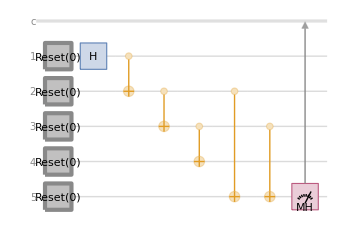

```mathematica
QECCatState[4]["Diagram"]
```

The property that matters is that the translation neither drops nor invents anything: one instruction, one operator. Resets and measurements survive ("M" -> q is the identity in the framework, so "Measurement" -> q is used), and Sdg is one box, not three S:

```mathematica
With[{g = QECTransversalGate[steane, "S"]},
    {Length[g["Instructions"]], Length[g["QuantumCircuitOperator"]["Operators"]]}]
```

{7,7}

## Step 3: a code as quantum operations

This is the core of the redesign. The theory of error correction (Knill–Laflamme–Viola) describes a code with five objects: an encoding isometry, a projector onto the code space, a syndrome measurement, a recovery per syndrome and, composing all of it, a channel on the logical qubit. Before, the layer gave none of them; now a code gives them all. The new file is Operational.wl.

Nothing new was invented to hold them. The framework already had an object for each of these ideas, and each property returns that object:

| property | returns | the framework object that already meant
       | code["Encoder"] | QuantumOperator | a linear map between qubits (here the isometry V, 1 qubit in, n out)
       | code["Codewords"] | a list of QuantumState | a state
       | code["Codespace"] | QuantumOperator | an operator (here the projector P==V V^†)
       | code["SyndromeMeasurement"] | QuantumMeasurementOperator | a measurement with one projector per outcome
       | code["Recovery", s] | QuantumChannel | a channel (here one Kraus operator, the correcting Pauli)
       | code["LogicalChannel", noise] | QuantumChannel | a channel (here on the logical qubit)
       | noise["QuantumChannel"] | QuantumChannel | a channel (now for every Pauli model, not only the named ones)

Asked directly:

```mathematica
Head /@ <|
    "Encoder" -> bitFlip["Encoder"],
    "Codewords" -> First[bitFlip["Codewords"]],
    "Codespace" -> bitFlip["Codespace"],
    "SyndromeMeasurement" -> bitFlip["SyndromeMeasurement"],
    "Recovery" -> bitFlip["Recovery", {1, 1}],
    "LogicalChannel" -> bitFlip["LogicalChannel", QECNoiseModel["BitFlip", 1/10]],
    "noise[\"QuantumChannel\"]" -> QECNoiseModel["BitFlip", 1/10]["QuantumChannel"]|>
```

<|Encoder→QuantumOperator,Codewords→QuantumState,Codespace→QuantumOperator,SyndromeMeasurement→QuantumMeasurementOperator,Recovery→QuantumChannel,LogicalChannel→QuantumChannel,noise["QuantumChannel"]→QuantumChannel|>

Because they are the framework's own objects, the framework's own operations work on them without any QEC-specific glue. The whole correction cycle can be run by hand: encode a framework state, hit it with a framework gate, measure the syndrome, apply the recovery — every step is just applying one framework object to another:

```mathematica
Module[{psi, hit, fixed, v},
    psi = bitFlip["Encoder"][QuantumState["+"]];          (* QuantumOperator on a QuantumState *)
    hit = QuantumOperator["X", {2}][psi];                  (* an ordinary framework gate as the error *)
    fixed = bitFlip["Recovery", bitFlip["Syndrome", "IXI"]][QuantumState[hit["DensityMatrix"]]];
    v = Normal[psi["StateVector"]];
    <|"encoded" -> Head[psi],
      "left alone by the projector" -> Chop[Normal[bitFlip["Codespace"][psi]["StateVector"]] - v] == ConstantArray[0, 8],
      "syndrome probabilities" -> Values[Normal[bitFlip["SyndromeMeasurement"][hit]["Probabilities"]]],
      "fidelity after recovery" -> Chop[Simplify[Conjugate[v] . Normal[fixed["DensityMatrix"]] . v]]|>]
```

<|encoded→QuantumState,left alone by the projector→True,syndrome probabilities→{0,0,0,1},fidelity after recovery→1|>

The rest of this step looks at each object in turn.

The encoder is the isometry V, as a QuantumOperator, from 1 logical qubit to 3 physical ones:

```mathematica
bitFlip["Encoder"]["Order"]
```

{{1,2,3},{1}}

Its columns are the codewords, and they are in the code's own logical basis: (|0)_L⟩ is the +1 eigenstate of the Z̄ that code["LogicalZ"] reports. That was not automatic. The five-qubit code's encoding circuit sends |00000⟩ to the -1 eigenstate of that Z̄ — a valid encoder, but with its labels swapped. Against what "Codewords" gives now:

```mathematica
Module[{z = Normal[QECPauli[First[five["LogicalZ"]]]["Matrix"]], raw, fixed},
    raw = Normal[QuantumCircuitOperator[Join[Table["I" -> q, {q, 5}], five["EncodingGates"]]][
        "QuantumOperator"]["MatrixRepresentation"]][[All, 1]];
    fixed = Normal[First[five["Codewords"]]["StateVector"]];
    <|"circuit alone" -> Simplify[Conjugate[raw] . z . raw],
      "Codewords" -> Simplify[Conjugate[fixed] . z . fixed]|>]
```

<|circuit alone→-1,Codewords→1|>

The projector is P==V V^†. It is checked against ∏_i (1+g_i)/2, the same projector built without the encoder:

```mathematica
Module[{p = Normal[bitFlip["Codespace"]["MatrixRepresentation"]], gens, one = IdentityMatrix[8]},
    gens = Normal[QECPauli[#]["Matrix"]] & /@ bitFlip["Generators"];
    p == Fold[#1 . (one + #2) / 2 &, one, gens]]
```

True

The syndrome measurement is a QuantumMeasurementOperator with one projector per syndrome. An X on the middle qubit trips both checks, syndrome {1,1}, the fourth outcome; and the recovery for that syndrome gives the codeword back:

```mathematica
Module[{zero = First[bitFlip["Codewords"]], hit},
    hit = QuantumOperator["IXI"][zero];
    <|"syndrome" -> bitFlip["Syndrome", "IXI"],
      "outcome probabilities" -> Values[Normal[bitFlip["SyndromeMeasurement"][hit]["Probabilities"]]],
      "recovered" -> Chop[Normal[bitFlip["Recovery", {1, 1}][QuantumState[hit["DensityMatrix"]]]["DensityMatrix"]] -
          Normal[zero["DensityMatrix"]]] == ConstantArray[0, {8, 8}]|>]
```

<|syndrome→{1,1},outcome probabilities→{0,0,0,1},recovered→True|>

The same measurement can be asked of the syndrome circuit: QECSyndromeCircuit[code]["SyndromeMeasurement"].

These four objects are dense — of size 2^n — and stop at $QECDenseQubitLimit (10 qubits by default) with a message saying what to use instead:

```mathematica
Block[{$QECDenseQubitLimit = 5}, steane["Encoder"]]
```

QECCode::dense: Encoder materializes a dense object on 7 qubits, above $QECDenseQubitLimit = 5. The logical channel, the Knill-Laflamme matrix and the detector model carry the same information without it; raise $QECDenseQubitLimit to force it.

$Failed

### The logical channel

Encoding, applying the noise, measuring the syndrome, recovering and decoding is one channel on the logical qubit. Building it literally goes through a 4^n-dimensional superoperator. But for Pauli noise on a stabilizer code the net result is always a logical Pauli, so the logical channel is a Pauli channel with 4^k weights, and those weights are exactly the coset probabilities the maximum-likelihood decoder already computed. So it comes out exact, symbolic, and cheap:

```mathematica
bitFlip["LogicalPauliProbabilities", QECNoiseModel["BitFlip", p]]
```

<|I→(-1+p)^2 (1+2 p),X→(3-2 p) p^2,Y→0,Z→0|>

This is decision A in one line: the logical error rate is one minus the identity weight, and the two agree coefficient for coefficient:

```mathematica
With[{noise = QECNoiseModel["Depolarizing", p]},
    Simplify[1 - steane["LogicalPauliProbabilities", noise]["I"] - QECLogicalErrorRate[steane, noise]]]
```

0

code["LogicalChannel", noise] is the same thing as a QuantumChannel on the logical qubit, ready to compose with anything else in the framework:

```mathematica
With[{ch = steane["LogicalChannel", QECNoiseModel["Depolarizing", 1/10]]}, {Head[ch], ch["Order"]}]
```

{QuantumChannel,{{0,1},{1}}}

It is a code-capacity object: with circuit-level noise the checks themselves fail, the cycle is no longer one channel, and the answer is Missing, pointing to the detector model.

### Noise as a channel

Noise can also be given in the framework's own terms. A one-qubit QuantumChannel that is a Pauli channel is read back as a noise model and is accepted everywhere a noise model is:

```mathematica
{QECNoiseModel[QuantumChannel["Depolarizing"[q]]]["Probabilities"],
 Expand[QECLogicalErrorRate[QECCode["Repetition", 3], QuantumChannel["BitFlip"[p]]]]}
```

{{1-(3 q)/4,q/4,q/4,q/4},3 p^2-2 p^3}

A channel that is not Pauli is refused with its reason, rather than approximated silently:

```mathematica
QECNoiseModel[QuantumChannel["AmplitudeDamping"[g]]]
```

QECNoiseModel::notpauli: QuantumChannel[…] is not a one-qubit Pauli channel; only Pauli noise has a description on a stabilizer code. Twirl it first if its Pauli approximation is what you want.

$Failed

And the other way round: noise["QuantumChannel"] used to work only for the named channels; it now works for every Pauli model.

### Knill–Laflamme

The underlying question — does the code correct this set of errors? — is the Knill–Laflamme condition. For Pauli errors it is decided on symplectic rows, without forming any 2^n vector, so it has no size limit. When it fails, it names the pair that breaks it and the logical operator their product is:

```mathematica
{bitFlip["KnillLaflammeMatrix", {"III", "XII", "IXI", "IIX"}],
 bitFlip["KnillLaflammeMatrix", {"XII", "IXX"}]}
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},Missing[NotCorrectable,<|Errors→{XII,IXX},Product→XXX|>]}

Asked of every error up to a weight, it reads off the distance:

```mathematica
Table[steane["CorrectableQ", "Weight"[t]], {t, 0, 2}]
```

{True,True,False}

The names "Codewords", "KnillLaflammeMatrix" and "CorrectableQ" are the ones the bosonic plan chose (Bosonic-QEC-PartA-Spec.md), so a qubit code and an oscillator code answer the same questions the same way.

## Step 4: the rate and the decoders

### One return type

Before, QECLogicalErrorRate returned a number, except when the circuit had heralds: then it returned an Association with "Rate", "Acceptance", and so on. The caller had to know that in advance. Now it always returns the rate:

```mathematica
Head /@ {QECLogicalErrorRate[steane, QECNoiseModel["Depolarizing", 1/10]],
    QECLogicalErrorRate[bitFlip, QECNoiseModel["Circuit", 1/1000], "Rounds" -> 1]}
```

{Rational,Rational}

The full report comes with All, with the same keys whether or not anything was post-selected (without heralds the acceptance is 1 and the failure is the rate):

```mathematica
QECLogicalErrorRate[steane, QECNoiseModel["Depolarizing", 1/10], All]
```

<|Rate→13147289/113906250,Acceptance→1,Failure→13147289/113906250|>

And the detector model, which is where heralds come from, answers the same as properties:

```mathematica
With[{dem = QECDetectorModel[bitFlip, QECNoiseModel["Circuit", 1/1000], 1]},
    {dem["LogicalErrorRate"] === QECLogicalErrorRate[bitFlip, QECNoiseModel["Circuit", 1/1000], "Rounds" -> 1],
     dem["Acceptance"]}]
```

{True,1}

### QECDecoder

There were three decoders inside the layer — the minimum-weight table, maximum likelihood over cosets, and the detector model's rule — but they could only be chosen with a string. Now they are objects:

```mathematica
With[{d = QECDecoder[steane]}, {d["Method"], d["Decode", {0, 0, 0, 1, 1, 1}]}]
```

{MinimumWeight,IIIIIIX}

QECDecoder[code, noise] is maximum likelihood (or, at circuit level, the detector model's decoder) and QECDecoder[dem] is the detector model's rule. None of them re-implements anything: they call the same function that already decoded, so the herald filter that moved the exponent from 1.73 to 1.965 is kept, and a test checks it table against table.

The fourth form is the way in for any other decoder: QECDecoder[code, f] wraps a function from syndrome to correction (PyMatching through ExternalEvaluate, a neural network, a lookup), and the rate scores it with the same machinery as the others. The decoder that never corrects anything fails whenever anything happens:

```mathematica
Simplify[QECLogicalErrorRate[bitFlip, QECNoiseModel["BitFlip", p],
    "Decoder" -> QECDecoder[bitFlip, If[# === {0, 0}, "III", Missing[]] &]]]
```

p (3-3 p+p^2)

## Step 5: the renames

All in one step, so the API breaks once and not several times:

| before | now
       | QECPauliVector[p] | QECPauli[p]["Vector"]
       | QECPauliString[p] | QECPauli[p]["String"]
       | QECPauliWeight[p] | QECPauli[p]["Weight"]
       | QECPauliPhase[p] | QECPauli[p]["Phase"]
       | QECPauliCommuteQ[p, q] | QECPauli[p]["CommuteQ", q]
       | QECPauliProduct[p, q] | QECPauli[p]["Product", q] or QECPauli[p] ** QECPauli[q]
       | QECFaultTolerant | QECFaultTolerantCircuit
       | QECStimCircuit | QECStim, plus dem["StimString"]
       | code["StimCircuit"] | code["Stim"]
       | QECCodeCatalog[] | QECCode["Catalog"]
       | QECClassicalHammingMatrix | internal; QECCode["Hamming", r] builds the quantum code

QECPauliQ stays as it is: it is the guard.

### QECPauli

A Pauli is now one object. It prints as its string and holds its row:

```mathematica
QECPauli["XZZXI"]
```

QECPauli[XZZXI]

Its properties are the six former functions, plus some that did not exist:

```mathematica
With[{P = QECPauli["-iXY"]},
    <|"String" -> P["String"], "Vector" -> P["Vector"], "Weight" -> P["Weight"], "Phase" -> P["Phase"],
      "Support" -> P["Support"], "HermitianQ" -> P["HermitianQ"]|>]
```

<|String→-iXY,Vector→{1,1,0,1,3},Weight→2,Phase→3,Support→{1,2},HermitianQ→False|>

The product carries the phase in Z_4, as before:

```mathematica
{(QECPauli["X"] ** QECPauli["Z"])["String"], QECPauli["XZZXI"]["CommuteQ", "IXZZX"]}
```

{-iY,True}

And a QECPauli is accepted wherever a string or a row was, and converts to the framework's objects:

```mathematica
{five["Syndrome", QECPauli["XIIII"]] === five["Syndrome", "XIIII"],
 Head[QECPauli["XZ"]["QuantumOperator"]]}
```

{True,QuantumOperator}

Underneath nothing changed shape: the row functions still exist in PackageScope with their original definitions, only under internal names (pauliVector, pauliProduct, …). The object wraps the row; it does not replace it.

### The constructions, also as properties

```mathematica
{steane["RemoveQubit"]["Parameters"],
 bitFlip["Concatenate", QECCode["PhaseFlipCode"]] === QECConcatenate[bitFlip, QECCode["PhaseFlipCode"]],
 Head[QECCode["Catalog"]]}
```

{{6,2,2},True,Dataset}

### The old names still work, for one more release

The eleven retired names (ten functions and the "StimCircuit" property) live in Deprecated.wl: they return exactly what they returned before and say, once per session, what to use instead:

```mathematica
QECPauliVector["XZ"]
```

QECPauliVector::qecdeprecated: QECPauliVector is deprecated and will be removed in the next release; use QECPauli[p][Vector] instead.

{1,0,0,1,0}

The second time there is no warning, so that a loop over a thousand Paulis does not print a thousand messages:

```mathematica
QECPauliVector["ZX"]
```

{0,1,1,0,0}

### The public surface

```mathematica
Module[{all = Names["Wolfram`QuantumFramework`QEC`*"], old, limits},
    old = {"QECPauliVector", "QECPauliString", "QECPauliWeight", "QECPauliCommuteQ", "QECPauliProduct",
        "QECPauliPhase", "QECFaultTolerant", "QECStimCircuit", "QECCodeCatalog", "QECClassicalHammingMatrix"};
    limits = Select[all, StringStartsQ[#, "$"] &];
    <|"public functions" -> Complement[all, old, limits], "limits" -> limits|>]
```

<|public functions→{QECCatState,QECClearCache,QECCliffordHierarchyLevel,QECCode,QECConcatenate,QECDecoder,QECDetectorModel,QECErrorCorrection,QECFaultTolerantCircuit,QECLogicalErrorRate,QECNoiseModel,QECPasteCodes,QECPauli,QECPauliMeasurement,QECPauliQ,QECPseudothreshold,QECRegister,QECRemoveQubit,QECStim,QECSyndromeCircuit,QECTransversalGate},limits→{$QECDecoderSubsetLimit,$QECDenseQubitLimit,$QECExactDetectorLimit,$QECExactEnumerationLimit,$QECStabilizerGroupLimit}|>

There were 26 functions at the start. It is not the "about 16" the audit estimated, because QECDecoder was added and the three constructions stayed functions (decision B).

## Step 6: transversal gates

Transversal.wl had the gate matrices copied by hand from the framework; a copy is a second convention that can drift. They are now read from QuantumOperator at load time:

```mathematica
Normal[QuantumOperator["S"]["Dagger"]["MatrixRepresentation"]] ===
    Wolfram`QuantumFramework`QEC`Transversal`PackagePrivate`$transversalGateMatrix["Sdg"]
```

True

The audit also asked for a primitive the framework does not have: conjugating a Pauli through a Clifford while keeping its phase. The kernel was not touched; it is written up as a proposal in QF-Clifford-Conjugation-Proposal.md. CliffordChannel already holds the table needed; what is missing is a constructor from a Clifford QuantumOperator and a cc["Conjugate", P] query.

## Step 7: documentation and tests

StabilizerCodes has two new sections (a code as quantum operations, and decoders as objects) and six new rows in its table of checks.

QECCoreInternals has three new sections: Operational.wl, Decoder.wl and Deprecated.wl.

All three tech notes use the new notation throughout; their 262 cells were validated and the notebooks rebuilt.

The README, the roadmap and the plan carry the new numbers; the plan has a status column for each of the audit's 16 observations.

|  | at the start | now
       | tests | 593 | 687
       | test files | 19 | 23
       | public functions | 26 | 19 (+ 4 $ limits)
       | files in QECCore/ | 21 | 25

New files: Gadget.wl, Operational.wl, Decoder.wl, Deprecated.wl, and the tests Gadget.wlt, Operational.wlt, Decoder.wlt, Surface.wlt. Nothing in QuantumFramework/Kernel/ was modified.

## One finding

The five-qubit code's encoder uses its own labels. Shown above: the encoding circuit produces the -1 eigenstate of the code's Z̄. Encoder.wl was not changed, because the circuit is still valid and is what the extraction and Stim consume; the new "Encoder" corrects it, and a test pins V^†Z̄ V==Z and V^†X̄ V==X on five codes.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

## Metadata

### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/APIRedesignChanges

### Keywords

quantum error correction

API redesign

QECPauli

QECDecoder

logical channel

Knill-Laflamme

encoder

deprecation